# Nutation of a Top

```mathematica
Quit[]
```

```mathematica
L=1/2 λ1(ϕdot^2 Sin[θ]^2+θdot^2)+1/2 λ3 (ψdot+ϕdot Cos[θ])^2-M g R Cos[θ]
rule={θ->θ[t],ϕ->ϕ[t],ψ-> ψ[t],θdot->θ'[t],ϕdot-> ϕ'[t],ψdot-> ψ'[t]};
dLdθ= D[L,θ]/.rule
dLdϕ=0
dLdψ=0
pϕ= D[L,ϕdot]/.rule
pθ= D[L,θdot]/.rule
pψ= D[L,ψdot]/.rule
```

-g M R Cos[θ]+1/2 λ3 (ψdot+ϕdot Cos[θ])^2+1/2 λ1 (θdot^2+ϕdot^2 Sin[θ]^2)

g M R Sin[θ[t]]+λ1 Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2-λ3 Sin[θ[t]] ϕ'[t] (Cos[θ[t]] ϕ'[t]+ψ'[t])

0

0

λ1 Sin[θ[t]]^2 ϕ'[t]+λ3 Cos[θ[t]] (Cos[θ[t]] ϕ'[t]+ψ'[t])

λ1 θ'[t]

λ3 (Cos[θ[t]] ϕ'[t]+ψ'[t])

```mathematica
ϕeq=dLdϕ== D[pϕ,t]
ψeq=dLdψ== D[pψ,t]
θeq=dLdθ== D[pθ,t]
```

0==2 λ1 Cos[θ[t]] Sin[θ[t]] θ'[t] ϕ'[t]-λ3 Sin[θ[t]] θ'[t] (Cos[θ[t]] ϕ'[t]+ψ'[t])+λ1 Sin[θ[t]]^2 ϕ''[t]+λ3 Cos[θ[t]] (-Sin[θ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] ϕ''[t]+ψ''[t])

0==λ3 (-Sin[θ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] ϕ''[t]+ψ''[t])

g M R Sin[θ[t]]+λ1 Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2-λ3 Sin[θ[t]] ϕ'[t] (Cos[θ[t]] ϕ'[t]+ψ'[t])==λ1 θ''[t]

```mathematica
λ1=1.5*10^(-4);
λ3=2.5*10^(-4);
M=.200;
g=9.8;
R=0.05;
```

```mathematica
tmax=1;
phidot01=10;
phidot02=30;
sol1=NDSolve[{θeq,ϕeq,ψeq,ψ[0]==0,θ[0]==0.2,ϕ[0]==0,ψ'[0]==20,θ'[0]==0,ϕ'[0]==phidot02},{θ[t],ϕ[t],ψ[t]},{t,0,tmax}]
```

{{θ[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t],ψ[t]→InterpolatingFunction[…][t]}}

```mathematica
θ[t_]=θ[t]/.sol1[[1]];
ϕ[t_]=ϕ[t]/.sol1[[1]];
ψ[t_]=ψ[t]/.sol1[[1]];
```

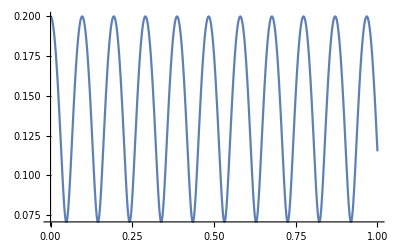

```mathematica
Plot[θ[t],{t,0,tmax}]
```

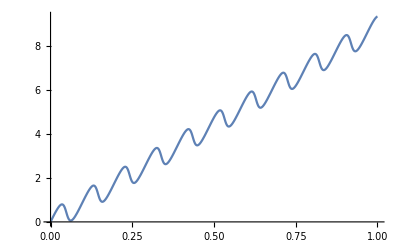

```mathematica
Plot[ϕ[t],{t,0,tmax}]
```

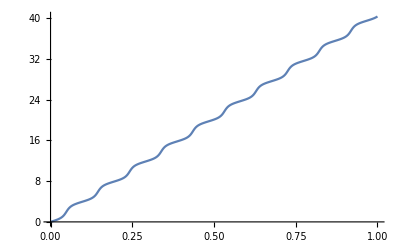

```mathematica
Plot[ψ[t],{t,0,tmax}]
```

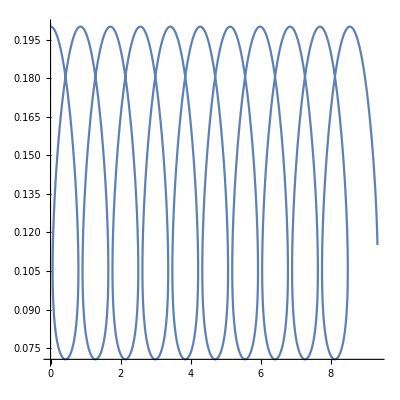

```mathematica
ParametricPlot[{ϕ[t],θ[t]},{t,0,tmax},AspectRatio->1]
```

```mathematica
ParametricPlot3D[{Sin[θ[t]] Cos[ϕ[t]],Sin[θ[t]] Sin[ϕ[t]],Cos[θ[t]]},{t,0,tmax},PlotStyle->Red,PlotRange->Automatic]
```

-Graphics3D-